```mathematica
Plot [x^2, {x,0,1}, Filling -> Axis]
```

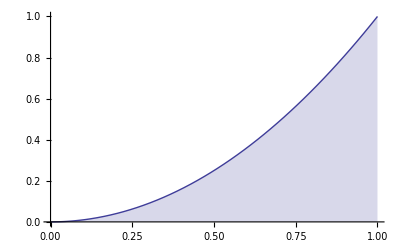

```mathematica
Plot [ {x^2, (Floor [10*x]/10)^2}, {x,0,1}, PlotStyle -> {Red, Blue}, Filling -> {1 -> { Axis, Opacity[1/10]}, 2 -> {Axis, opacity [2/10]}}]
```

-Graphics-

```mathematica
∑_(i=1)^10 (i-1/10)^2 * (1/10)
```

3741/100

```mathematica
∑_(i=1)^10 ((i-1)/10)^2 * (1/10)//N
```

0.285

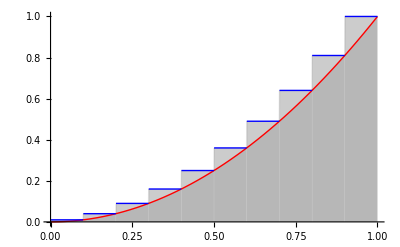

```mathematica
Plot [ {x^2, (Floor [10*x + 1]/10)^2}, {x,0,1}, PlotStyle -> {Red, Blue}, Filling -> {1 -> { Axis, Opacity[1/10]}, 2 -> {Axis, Opacity [2/10]}}]
```

```mathematica
∑_(i=1)^10 (i/10)^2 * (1/10)//N
```

0.385

```mathematica
Plot [ {x^2, ((Floor [10*x ]+ 5)/10)/10)^2}, {x,0,1}, PlotStyle -> {Red, Blue}, Filling -> {1 -> { Axis, Opacity[1/10]}, 2 -> {Axis, Opacity [2/10]}}]
```

```mathematica
areaR [n_] := ∑_(i=1)^n (i/n)^2 * (1/n)
Table [ areaR [n] // N, {n, 10, 100, 10}]
```

{0.385,0.35875,0.350185,0.345938,0.3434,0.341713,0.34051,0.339609,0.338909,0.33835}

```mathematica
(1+n) * (1 + 2* n)/ 6* (n^2)
```

1/6 n^2 (1+n) (1+2 n)

```mathematica
Limit [areaR [n], n->g
```